```mathematica
c0=ParametricPlot[{Re[Cos[t]],Re[Sin[t]]},{t,0,2 Pi},PlotStyle->Red];
```

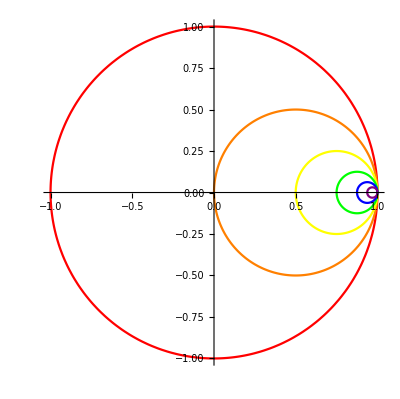

```mathematica
ϕ[z_]:=1/2z+1/2;
ϕ2[z_]:=ϕ[ϕ[z]];
ϕ3[z_]:=ϕ[ϕ[ϕ[z]]];
ϕ4[z_]:=ϕ[ϕ[ϕ[ϕ[z]]]];
ϕ5[z_]:=ϕ[ϕ[ϕ[ϕ[ϕ[z]]]]];
c1=ParametricPlot[{Re[ϕ[Re[Cos[t]]+I Re[Sin[t]]]],Im[ϕ[Re[Cos[t]]+I Re[Sin[t]]]]},{t,0,2 Pi},PlotStyle->Orange];
c2=ParametricPlot[{Re[ϕ2[Re[Cos[t]]+I Re[Sin[t]]]],Im[ϕ2[Re[Cos[t]]+I Re[Sin[t]]]]},{t,0,2 Pi},PlotStyle->Yellow];
c3=ParametricPlot[{Re[ϕ3[Re[Cos[t]]+I Re[Sin[t]]]],Im[ϕ3[Re[Cos[t]]+I Re[Sin[t]]]]},{t,0,2 Pi},PlotStyle->Green];
c4=ParametricPlot[{Re[ϕ4[Re[Cos[t]]+I Re[Sin[t]]]],Im[ϕ4[Re[Cos[t]]+I Re[Sin[t]]]]},{t,0,2 Pi},PlotStyle->Blue];
c5=ParametricPlot[{Re[ϕ5[Re[Cos[t]]+I Re[Sin[t]]]],Im[ϕ5[Re[Cos[t]]+I Re[Sin[t]]]]},{t,0,2 Pi},PlotStyle->Purple];
Show[c0,c1,c2,c3,c4,c5]
```